Based on Laura’s notebook

```mathematica
Quit[];
```

#### Plots Styles

```mathematica
colours={ColorData[10,6],ColorData[10,1],ColorData[10,5],ColorData[10,3],ColorData[10,8],ColorData[10,2],ColorData[10,7],ColorData[10,4],ColorData[10,9]}
```

{RGBColor[0.3176470588235294, 0.49019607843137253, 0.0784313725490196],RGBColor[0.6980392156862745, 0.01568627450980392, 0.],RGBColor[0.7254901960784313, 0.8, 0.07058823529411765],RGBColor[0.9372549019607843, 0.6274509803921569, 0.16862745098039217],RGBColor[0.3607843137254902, 0.40784313725490196, 0.5333333333333333],RGBColor[0.9215686274509803, 0.49411764705882355, 0.43137254901960786],RGBColor[0.17254901960784313, 0.3607843137254902, 0.07058823529411765],RGBColor[0.9921568627450981, 0.8156862745098039, 0.49019607843137253],RGBColor[0.22745098039215686, 0.23921568627450981, 0.45098039215686275]}

```mathematica
basicdisp={AxesStyle->Directive[Black,12],LabelStyle->Directive[Black,12]};
```

### Intro, always run

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/stasya/prj/coscattering/Laura/Xsections

```mathematica
Limp[m1_,m2_,m3_,m4_]:=Module[{E1cmt, E3cmt, E2cmt,p1cmt,p3cmt,p2cmt,tpt,tmt,p1dcmt},
E1cmt=(s+m1^2-m2^2)/(2Sqrt[s]);
p1cmt=Sqrt[E1cmt^2-m1^2];
E2cmt=(s+m2^2-m1^2)/(2Sqrt[s]);
p2cmt=Sqrt[E2cmt^2-m2^2];
E3cmt=(s+m3^2-m4^2)/(2Sqrt[s]);
p3cmt=Sqrt[E3cmt^2-m3^2];
tmt=(m1^2-m2^2-m3^2+m4^2)^2/(4s)-(p1cmt-p3cmt)^2;
tpt=(m1^2-m2^2-m3^2+m4^2)^2/(4s)-(p1cmt+p3cmt)^2;
{tpt,tmt,p1cmt,p2cmt}
]
```

```mathematica
Gammu=10^(-18) (*width of muon in GeV*)
num=.
num0={mph->1000,mX->10,mH->150,mmu->0.105,pref->1,lam->1,mwidth->Gammu*mmu}
num=Join[num0,{s->(mmu+mph)^2*del,del->10.}]
numX=Join[num0,{s->(mmu+mph)^2*del,del->XX}]
```

1/1000000000000000000

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000}

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000,s→del (mmu+mph)^2,del→10.}

{mph→1000,mX→10,mH→150,mmu→0.105,pref→1,lam→1,mwidth→mmu/1000000000000000000,s→del (mmu+mph)^2,del→XX}

```mathematica
assum={mx>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&test>0&&nv>0&&x>0&&Ex>0&&Eb>0&&T>0&&Element[{mx,MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,test,nv,x,Ex,Eb,T}, Reals]}
```

{mx>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&test>0&&nv>0&&x>0&&Ex>0&&Eb>0&&T>0&&(mx|MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|test|nv|x|Ex|Eb|T)∈ℝ}

```mathematica
params={MZp->20.,MD1->1.,MD2->1.02,epsilon->1.*^-6,aXM1->127.89999999999999,swsq->0.225,aEWM1->127.89999999999999,MZ->91.188,ttheta->0.00001,ME->0.0005110000000000001,cw->pow[1-swsq,0.5],sw->pow[swsq,0.5],aEW->pow[aEWM1,-1],EE->2 pow[aEW,0.5] pow[π,0.5],aX->pow[aXM1,-1],gX->2 pow[aX,0.5] pow[π,0.5],chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-0.5],SignAux->(MZ-MZp) pow[pow[MZ-MZp,2],-0.5],DZaux->SignAux pow[pow[MZ,4]+pow[MZp,4]-2 pow[MZ,2] pow[MZp,2] (1+2 pow[eta,2] pow[sw,2]),0.5],DZ->0.5 pow[MZ,-2] pow[MZp,-2] (-DZaux pow[MZ,2]+pow[MZ,4]+pow[MZp,4]+pow[MZp,2] (-DZaux-2 pow[eta,2] pow[MZ,2] pow[sw,2])),taAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-0.5 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],0.5]),ca->pow[1+pow[ta,2],-0.5],sa->ta pow[1+pow[ta,2],-0.5],ctheta->pow[1+pow[ttheta,2],-0.5],stheta->ttheta pow[1+pow[ttheta,2],-0.5]}/.pow->Power;
paramsnoMD2=Drop[params,{3}];
```

```mathematica
GeVm2toPb=0.389379 10^9
```

3.89379×10^8

```mathematica
(* to use Izaguare notations*)
reply={alphX->y/eps^2*MZp^4/MD1^4};
(* to use sa in the small epsilon limit*)
replcoann={gX^2->alphX*4*Pi,EE^2->alph*4*Pi,ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
```

```mathematica
(*not used
replta={chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-1/2],SignAux->(MZ-MZp) pow[pow[MZ-MZp,2],-1/2],DZaux->SignAux pow[pow[MZ,4]+pow[MZp,4]-2 pow[MZ,2] pow[MZp,2] (1+2 pow[eta,2] pow[sw,2]),1/2],DZ->1/2pow[MZ,-2] pow[MZp,-2] (-DZaux pow[MZ,2]+pow[MZ,4]+pow[MZp,4]+pow[MZp,2] (-DZaux-2 pow[eta,2] pow[MZ,2] pow[sw,2])),taAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-1/2 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],1/2]),ca->pow[1+pow[ta,2],-1/2],sa->ta pow[1+pow[ta,2],-1/2]}/.pow->Power;
repltanoDZ={chi->epsilon pow[cw,-1],eta->chi pow[1-pow[chi,2],-1/2],StaAux->-1+DZ+pow[eta,2] pow[sw,2],ta->-1/2 pow[eta,-1] pow[sw,-1] (taAux+SignAux pow[4 pow[eta,2] pow[sw,2]+pow[taAux,2],1/2]),ca->pow[1+pow[ta,2],-1/2],sa->ta pow[1+pow[ta,2],-1/2]}/.pow->Power;
*)
```

## Getting cross - section chi1 e-> chi2 e Zp (test=(m2-m1)/m1, vrel=test x nv) BEST OPTION

### getting M^2

```mathematica
<<"m-files/sum_22.m"
<<"m-files/symbc1ec2e-vSam-Zp.m"
```

```mathematica
assum={ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&Element[{MD1,MD2,MZ,MZp,sa,sw,ca,eta,chi,vrel,del,ME,T}, Reals]}
```

{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME|T)∈ℝ}

```mathematica
m1=Simplify[Sqrt[SC[p1,p1]],assum]
m2=Simplify[Sqrt[SC[p2,p2]],assum]
m3=Simplify[Sqrt[SC[p3,p3]],assum]
m4=Simplify[Sqrt[-2*SC[p2,p3]-(-2*SC[p1,p2]+2*SC[p1,p3])+m1^2+m2^2+m3^2],assum]
mylim=Limp[m1,m2,m3,m4];
tm=mylim[[1]]
tp=mylim[[2]]
p1cm=mylim[[3]]//Simplify
p1=.
```

MD1

ME

ME

MD2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))+√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

((MD1^2+MD2^2-2 ME^2)^2)/(4 s)-(√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))-√(-ME^2+((-MD2^2+ME^2+s)^2)/(4 s)))^2

√(-MD1^2+((MD1^2-ME^2+s)^2)/(4 s))

```mathematica
sig0=sig=1/(64Pi s)/p1cm^2/.ME->0;
Msq=sum/.{pow->Power}/.ME->0//Simplify
```

(ca^2 ctheta^2 EE^2 eta^2 gX^2 stheta^2 (cw^4 sa^2-2 cw^2 sa sw (ca eta+sa sw)+5 sw^2 (ca eta+sa sw)^2) (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/(4 chi^2 cw^2 sw^2 (-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* Amplitude squared in eps->0 limit, propto eps^2*)
Msq//.{ca->Sqrt[1-sa^2],chi->eps/cw,eta->(eps/cw)/Sqrt[1-(eps/cw)^2],sa->-sw eps/cw};
Series[%,{eps,0,2}]/.sw->Sqrt[1-cw^2];
Msqlim=SeriesCoefficient[%,2]*eps^2
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (2 MD1^3 MD2+s^2+2 MD1 MD2 (MD2^2-s-t)+MD1^2 (2 MD2^2-s-t)+t^2-MD2^2 (s+t)))/((-MD1^2-MD2^2+MZp^2+s+t)^2)

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
Msqlimc1c2=Msqlim/.MD2->MD1//Simplify
Msqlimc1c1
Msqlimc1c2/Msqlimc1c1
```

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/((-2 MD1^2+MZp^2+s+t)^2)

Msqlimc1c1

(2 ctheta^2 EE^2 eps^2 gX^2 stheta^2 (6 MD1^4+s^2+t^2-4 MD1^2 (s+t)))/(Msqlimc1c1 (-2 MD1^2+MZp^2+s+t)^2)

### getting xsections and testing limit MD2->MD1 analytics ok

```mathematica
(* cross-section*)
IntM=Integrate[Msq,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
sv=sig0*(IntMp-IntMm);
```

```mathematica
(* cross-section eps->0 limit, propto eps^2*)
IntM=Integrate[Msqlim,t];
IntMp=IntM/.t->tp/.ME->0;
IntMm=IntM/.t->tm/.ME->0;
svlim=sig0*(IntMp-IntMm);
```

```mathematica
(* the limit mx1=mx2 gived the same result at the level of amplitude squared and Xsection than in the c1 e->c1 e case above up to as (ctheta/stheta)^2 correction factor*)
svlimc1c2=svlim/.MD2->MD1//Simplify
svlimc1c1
Rsv=svlimc1c2/svlimc1c1
```

(ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s]))/(8 π (MD1^2-s)^2)

svlimc1c1

(ctheta^2 EE^2 eps^2 gX^2 stheta^2 (((MD1^2-s)^2 (MD1^4 (MZp^2+2 s)-2 MD1^2 s (MZp^2+2 s)+s (2 MZp^4+3 MZp^2 s+2 s^2)))/(MZp^2 s (MD1^4-2 MD1^2 s+s (MZp^2+s)))+2 (MZp^2+s) Log[MZp^2]-2 (MZp^2+s) Log[-2 MD1^2+MZp^2+MD1^4/s+s]))/(8 π (MD1^2-s)^2 svlimc1c1)

```mathematica
(*Weird, when I first give all params except M2 and then M2 it gives a different numerical result...*)
ptest=MD1/30/.params;
ss=Solve[p1cm==ptest,s]/.params
tpt=tp/.ss[[2,1]]//.params;
tmt=tm/.ss[[2,1]]//.params;
If[tpt>tmt,sv/.ss[[2,1]]//.params,-sv/.ss[[2,1]]//.params]*GeVm2toPb
If[tpt>tmt,sv/.ss[[2,1]]//.paramsnoMD2,-sv/.ss[[2,1]]//.paramsnoMD2]*GeVm2toPb/.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
svlim*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.paramsnoMD2/.params
(*test0*GeVm2toPb/.eps->epsilon/.ss[[2,1]]//.params
test*GeVm2toPb/.eps->epsilon/.ss[[2,1]]/.vrel->4*ptest/MD1//.params*)
```

{{s→0.935511},{s→1.06893}}

6.75237×10^-26

6.8679×10^-26

6.54179×10^-26

6.8679×10^-26

```mathematica
myvrel=4*ptest/MD1//.params
mys=MD1^2(1+myvrel/2)//.params
```

0.133333

1.06667

```mathematica
svlimc1c1*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
svlimc1c1*Rsv*GeVm2toPb/.eps->epsilon//.params//.ss[[2,1]]
```

3.89379×10^8 svlimc1c1

4.15061×10^-25

### getting series of xsection in test=(MD2-MD1)/MD1=test and vrel =2 (2+test) test+test2

```mathematica
Series[svlim//.{MD2->MD1(1+test),s->MD1^2(1+vrel/2),vrel->(4+2test)test+test2},{test,0,1},{test2,0,2}]//Normal;
svseries=Simplify[%,assum]
%*GeVm2toPb//.{alph->1/aEWM1,del->MD2-MD1,y->eps^2 MD1^4/MZp^4 aX,eps->epsilon,vrel->4*ptest/MD1,test->del/MD1,test2->vrel-(4+2test)test}//.params
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-1+2 test) test2^2)/(32 MZp^4 π)

6.19117×10^-26

```mathematica
Collect[svseries/.{test2-> vrel-(4+2test)test}/.vrel-> -(2 (MD1^2-s))/MD1^2/.test-> δ,s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 s stheta^2 (-1+2 δ) (-8/MD1^2-(4 δ (4+2 δ))/MD1^2))/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (-1+2 δ) (4+4 δ (4+2 δ)+δ^2 (4+2 δ)^2))/(32 MZp^4 π)

```mathematica
svseries//.replcoann//.reply
```

-(alph ctheta^2 π stheta^2 (-1+2 test) test2^2 y)/(2 MD1^2)

## Nastya’s edition

### Velocity and δ=(MD2-MD1)/MD1 expansion

#### Expanding in δ and test2=vrel-(4+2δ)δ

```mathematica
ClearAll[vrel];
```

```mathematica
σvSeries=Series[svlim//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2),vrel->(4+2δ)δ+test2},{δ,0,1},{test2,0,2}]//Normal//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 test2^2 (1-2 δ))/(32 MZp^4 π)

```mathematica
σvSeries=
Collect[Simplify[σvSeries/.test2->vrel-(4+2δ)δ,assum],vrel]
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2 (-1+2 δ))/(32 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ (2+δ) (-1+2 δ))/(8 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ^2 (2+δ)^2 (-1+2 δ))/(8 MZp^4 π)

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]
```

-(2 (MD1^2-s))/MD1^2

```mathematica
σvSeries=Collect[Simplify[σvSeries/.vrel-> vrels,assum],s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

#### Expanding in δ and vrel (cross-check)

```mathematica
σvSeries2=Series[svlim//.{MD2->MD1(1+δ),s->MD1^2(1+vrel/2)},{δ,0,1},{vrel,4δ+2 δ^2,2}]//Normal;
```

```mathematica
σvSeries2=Collect[Series[σvSeries2,{δ,0,1}],vrel](*same as when expanded in δ and test2*)
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ)/(4 MZp^4 π)+vrel^2 ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))

## Averaged cross section numerically, mx=MD1

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ,nDM,nbFermions,nbBosons]
```

```mathematica
nDM[x_]:=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions[x_]:=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons[x_]:=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
Plot3D[(mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ))/.{cosθ-> -1,mx-> 100},{Ex,100,10^6},{Eb,0,10^6},AxesLabel->{"Ex","Eb","smax"}]
```

-Graphics3D-

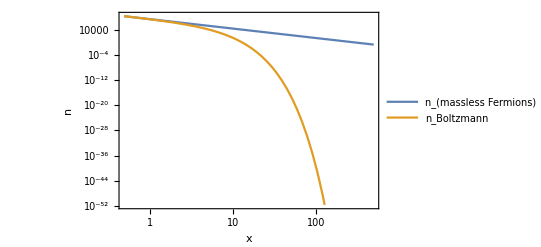

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbFermions[x]/.gb-> 1],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nDM[x]/.gb-> 1]},{x,0,500},Frame->True,FrameLabel->{"x","n"},PlotLegends-> {"n_(massless Fermions)","n_Boltzmann"}]
```

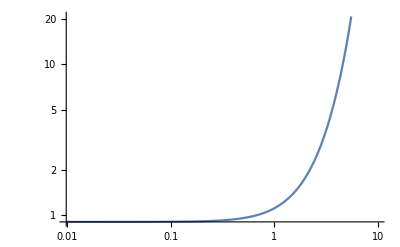

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},nbFermions[x]/nDM[x]/.gb-> 1]},{x,0,10}]
```

#### Full integral

```mathematica
ss=sfromθ/.{Eb->  (Ep+Em)/2,Ex-> (Ep-Em)/2}
```

mx^2+(Em+Ep) (1/2 (-Em+Ep)-cosθ √(1/4 (-Em+Ep)^2-mx^2))

```mathematica
Solve[s==ss/.cosθ-> -1,Em]//FullSimplify
```

{{Em→-(Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s},{Em→(-Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s}}

```mathematica
Solve[s==ss/.cosθ-> 1,Em]//FullSimplify
```

{{Em→-(Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s},{Em→(-Ep mx^2+√((Ep^2-s) (mx^2-s)^2))/s}}

```mathematica
sfromθ
```

mx^2+2 Eb (Ex-cosθ √(Ex^2-mx^2))

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
σvAveragedNR[x_]:=(x/m)/(8 m^4 BesselK[2,x]^2)NIntegrate[(σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞},WorkingPrecision->50]/.m-> MD1
```

```mathematica
σvAveragedFermionsN[x_]:=NIntegrate[(σvSeries(s-mx^2)1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T)HeavisideTheta[s-sfromθ/.cosθ-> 1]HeavisideTheta[-s+sfromθ/.cosθ->-1])/.mx-> MD1//.T-> MD1/x,{s,0,∞},{Eb,0,∞},{Ex,MD1,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->50]
```

```mathematica
listIntN=Transpose[{{1,10,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},σvAveragedFermionsN[#]&/@{1,10,50,100,500}]}]
```

NIntegrate::precw: The precision of the argument function ((ⅇ^(-Ex/100) (-10000+s) (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) HeavisideTheta[10000+2 Eb (Ex+√(-10000+Power[«2»]))-s] HeavisideTheta[-10000-2 Eb (Ex-√Plus[«2»])+s])/(1+ⅇ^(Eb/100))) is less than WorkingPrecision (50.).

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::precw: The precision of the argument function ((ⅇ^(-Ex/10) (-10000+s) (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) HeavisideTheta[10000+2 Eb (Ex+√(-10000+Power[«2»]))-s] HeavisideTheta[-10000-2 Eb (Ex-√Plus[«2»])+s])/(1+ⅇ^(Eb/10))) is less than WorkingPrecision (50.).

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

NIntegrate::precw: The precision of the argument function ((ⅇ^(-Ex/2) (-10000+s) (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) HeavisideTheta[10000+2 Eb (Ex+√(-10000+Power[«2»]))-s] HeavisideTheta[-10000-2 Eb (Ex-√Plus[«2»])+s])/(1+ⅇ^(Eb/2))) is less than WorkingPrecision (50.).

General::stop: Further output of NIntegrate::precw will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{1,0},{10,0},{50,0},{100,0},{500,0}}

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedFermionsN[10],10]]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0

```mathematica
Integrand=σvSeries(s-mx^2)1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T)HeavisideTheta[s-sfromθ/.cosθ-> 1]HeavisideTheta[-s+sfromθ/.cosθ->-1];
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,Ex=1000,Eb=10,s=20000},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10//N
```

2.45374×10^-48

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,Eb=10,s=20000,Ex= 1000},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10//N
```

2.45374×10^-48

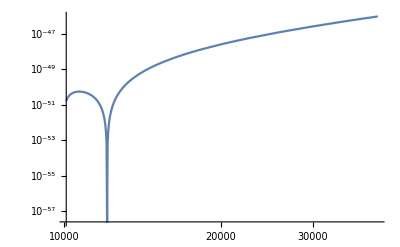

```mathematica
LogLogPlot[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1,Eb=10,Ex=1000},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10//N,{s,0,40000},PlotRange->All]
```

```mathematica
NIntegrate[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10,{Ex,100,∞},{Eb,0,∞},{s,0.,400000},WorkingPrecision->20]
```

```mathematica
NIntegrate[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},Integrand/.mx-> MD1//.T-> MD1/x]/.x-> 10,{Ex,100,∞},{Eb,0,∞},{s,0,400000},WorkingPrecision->50,MinRecursion -> 10,MaxRecursion -> 100]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 3.92597497871996460819423007017320407208822936258700981557421117126618739809253274306457139459406248×10^-6 and 5.633735126209796704218087467677040431210232698043520776267504648687490866007740514335887313488357772×10^-7 for the integral and error estimates.

3.925974978719964608194230070173204072088229362587×10^-6

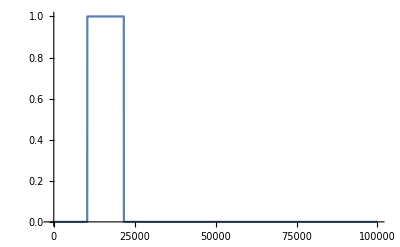

```mathematica
Plot[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,mx=100,δ=10^-1,Ex= 300,T=10,Eb=10},HeavisideTheta[s-sfromθ/.cosθ-> 1]HeavisideTheta[-s+sfromθ/.cosθ->-1]],{s,-1000,10^5}]
```

#### Numerical int over s

#### Analytically over s, then numerically

```mathematica
sfromθ
```

mx^2+2 Eb (Ex-cosθ √(Ex^2-mx^2))

```mathematica
σvSeries=-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel^2 (-1+2 δ))/(32 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ (2+δ) (-1+2 δ))/(8 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ^2 (2+δ)^2 (-1+2 δ))/(8 MZp^4 π);
```

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]
```

-(2 (MD1^2-s))/MD1^2

```mathematica
σvSeries=Collect[Simplify[σvSeries/.vrel-> vrels,assum],s]
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
Sint=Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum]
```

-(ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2)))/(3 MD1^2 MZp^4 π)

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},((2 π^2)/(nDM[x] nbFermions[x])Sint 1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1]
```

(49 ⅇ^(-(Ex x)/100) Eb^2 √(-10000+Ex^2) (121203 Ex-804 Eb (-10000+4 Ex^2)+12 Eb^2 (-10000 Ex+2 Ex^3)) x^4)/(145800000000000000000000000000 (1+ⅇ^((Eb x)/100)) π BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermionsSemiN[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/(ⅇ^(Eb/T)+1)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Ex,MD1,∞},{Eb,0,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]
σvAveragedFermionsSemiNNReorderred[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/ⅇ^(Eb/T)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Eb,0,∞},{Ex,MD1,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]

σvAveragedFermionsSemiNNR[x_]:=(2 π^2)/(nDM[x] nbFermions[x])NIntegrate[(Sint 1/ⅇ^(Eb/T)ⅇ^(-Ex/T))/.mx-> MD1/.T-> MD1/x/.gb-> 1,{Ex,MD1,∞},{Eb,0,∞},MinRecursion -> 10,MaxRecursion -> 100,WorkingPrecision->20]

σvAveragedNR[x_]:=(x/m)/(8 m^4 BesselK[2,x]^2)NIntegrate[(σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞},WorkingPrecision->20]/.m-> MD1
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiN[#]]&/@{1,20}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.000054931432057976757015,6.8329188095133730887×10^-9}

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNReorderred[#]]&/@{1,20}
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{0.00005650335886682345518,6.9965502622927172224×10^-9}

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedNR[0.01]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.1145×10^10}. NIntegrate obtained 1.44864×10^25 and 3.08889×10^22 for the integral and error estimates.

4527.24

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNRmassive[0.01]]
```

NIntegrate::precw: The precision of the argument function (1.04793×10^-15 ⅇ^(-0.0001 Eb-0.0001 Ex) Eb^2 √(-10000+Ex^2) (1.323×10^7 Ex-8400. Eb (-10000+4 Ex^2)+12 Eb^2 (-10000 Ex+2 Ex^3))) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5021.55

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNR[0.01]]
```

NIntegrate::precw: The precision of the argument function (1.04793×10^-15 ⅇ^(-0.0001 Eb-0.0001 Ex) Eb^2 √(-10000+Ex^2) (1.323×10^7 Ex-8400. Eb (-10000+4 Ex^2)+12 Eb^2 (-10000 Ex+2 Ex^3))) is less than WorkingPrecision (20.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

5021.55

```mathematica
listIntSemiN=Transpose[{{1,5,10,20,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiN[#]&/@{1,5,10,20,50,100,500}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1,0.000054931432057976757015},{5,2.7396933371509485649×10^-7},{10,4.404131011051305641×10^-8},{20,6.8329188095133730887×10^-9},{50,1.0603192542110393625×10^-9},{100,8.8246059634433136481×10^-10},{500,1.5321593835410300383×10^-9}}

```mathematica
listIntSemiNNR=Transpose[{{1,5,10,20,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsSemiNNR[#]&/@{1,5,10,20,50,100,500}]}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

{{1,0.00005650335886682345518},{5,2.7912867487207676271×10^-7},{10,4.4430799225606366807×10^-8},{20,6.9965502622927172224×10^-9},{50,1.2266273552035327948×10^-9},{100,1.018268607031666507×10^-9},{500,1.7099638027075202496×10^-9}}

```mathematica
listIntNR=Transpose[{{1,10,50,100,500},Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedNR[#]&/@{1,10,50,100,500}]}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{1,0.0000600423},{10,3.51956×10^-7},{50,1.06423×10^-7},{100,7.20259×10^-8},{500,0.}}

NIntegrate::precw: The precision of the argument function ((-40000+s) √s (5.75355×10^-8-9.51×10^-12 s+3.92975×10^-16 s^2) BesselK[1,0.0100013 √s]) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {2.1875158059697448829×10^6}. NIntegrate obtained 1.2666504379114081953×10^7 and 0.23711357362091467677 for the integral and error estimates.

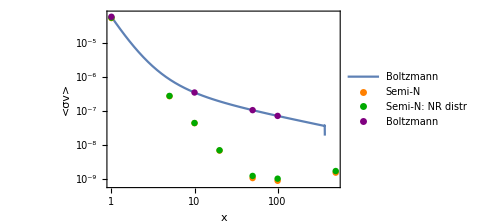

```mathematica
Show[{LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=10^-1},σvAveragedNR[x]]} ,{x,1,500},Frame->True,FrameLabel->{"x","<σv>"},PlotRange-> {{1,500},{7 10^-10,7 10^-5}},PlotLegends->{"Boltzmann"},ImageSize->Medium],ListLogLogPlot[listIntSemiN,PlotStyle->Orange,PlotLegends->{"Semi-N"}],ListLogLogPlot[listIntSemiNNR,PlotStyle->Darker[Green],PlotLegends->{"Semi-N: NR distr"}],ListLogLogPlot[listIntNR,PlotStyle->Purple,PlotLegends->{"Boltzmann"}]}]
```

## Analytical averaged cross section, no σ expansion, mx=MD1

#### Int over s, Eb & Ex

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

Integration over s

```mathematica
Sint=Collect[ Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum],{σ0,σ1,σ2}]
```

-1/(3 MD1^2 MZp^4 π)ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2))

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Integrate[Sint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum]
```

-1/(3 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (7/30 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+9/2 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+270 (2 Ex^3-Ex mx^2) T^5 Zeta[5])

```mathematica
EbintBosons=Integrate[Sint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum]
```

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
(*ExintFermions=Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum]*)
```

```mathematica
ConditionalExpression[-1/(30 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5])), Re[T]>0]
```

```mathematica
ExintFermions=-1/(30 MD1^2 MZp^4 π)ctheta^2 EE^2 eps^2 gX^2 mx^2 stheta^2 T^4 (-1+2 δ) (mx T BesselK[1,mx/T] (7 mx^2 π^4-7 MD1^2 π^4 (1+δ)^2+16200 T^2 Zeta[5])+BesselK[2,mx/T] (28 mx^2 π^4 T^2+45 mx^4 Zeta[3]+45 MD1^4 (1+δ)^4 Zeta[3]-2 MD1^2 (1+δ)^2 (14 π^4 T^2+45 mx^2 Zeta[3])+2700 mx^2 T^2 Zeta[5]+64800 T^4 Zeta[5]));
```

```mathematica
(*ExintFermions=12 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+2/15 mx^2 T^4 σ1 (7 mx π^4 T BesselK[1,mx/T]+28 π^4 T^2 BesselK[2,mx/T]+90 mx^2 BesselK[2,mx/T] Zeta[3])+2/15 mx^2 T^4 σ2 (14 mx^3 π^4 T BesselK[1,mx/T]+56 mx^2 π^4 T^2 BesselK[2,mx/T]+90 mx^4 BesselK[2,mx/T] Zeta[3]+32400 mx T^3 BesselK[1,mx/T] Zeta[5]+5400 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);*)
```

```mathematica
(*ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]*)
```

```mathematica
(*ExintBosons=16 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+16/15 mx^2 T^4 σ1 (mx π^4 T BesselK[1,mx/T]+4 π^4 T^2 BesselK[2,mx/T]+15 mx^2 BesselK[2,mx/T] Zeta[3])+16/15 mx^2 T^4 σ2 (2 mx^3 π^4 T BesselK[1,mx/T]+8 mx^2 π^4 T^2 BesselK[2,mx/T]+15 mx^4 BesselK[2,mx/T] Zeta[3]+4320 mx T^3 BesselK[1,mx/T] Zeta[5]+720 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);*)
```

```mathematica
(ExintFermions-ExintBosons)//FullSimplify
```

#### Putting together <σv>

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ,nbFermions,nbBosons,nDM,IntFermions]
```

```mathematica
nDM[x_]:=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions[x_]:=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons[x_]:=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
IntFermions[x_]:=ExintFermions/.mx-> MD1/.T-> MD1/x//FullSimplify
```

```mathematica
σvAveragedFermionsFunc[x_]:=(2 π^2)/(nDM[x] nbFermions[x])IntFermions[x]//FullSimplify
σvAveragedNR[x_]:=(x/m)/(8 m^4 BesselK[2,x]^2)NIntegrate[(σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞},WorkingPrecision->50]/.m-> MD1 (*non-relativistic medium frim Gondolo&Gelmini*)
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[30],10]]
```

7.20024×10^-10

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},σvAveragedFermionsFunc[30]]
```

7.20024×10^-10

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[500],10]]
```

4.919812404×10^-8

#### Plots

NIntegrate::precw: The precision of the argument function ((-40000+s) √s (14641/(81000000000 π)-(121 s)/(4050000000000 π)+s^2/(810000000000000 π)) BesselK[1,0.0100011 √s]) is less than WorkingPrecision (20.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {2.1875158059697448829×10^6}. NIntegrate obtained 1.266870127890115346×10^7 and 0.23718702339185046939 for the integral and error estimates.

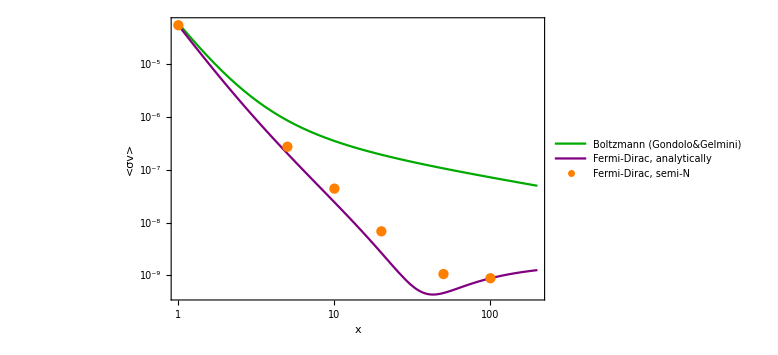

Export::infer: Cannot infer format of file Co-scattering cross-section.

$Failed

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},N[σvAveragedNR[x],10]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-1},σvAveragedFermionsFunc[x]]} ,{x,1,200},Frame->True,FrameLabel->{"x","<σv>"},ImageSize->Large,PlotStyle->{Darker[Green],Purple},PlotLegends->{"Boltzmann (Gondolo&Gelmini)","Fermi-Dirac, analytically"}],ListLogLogPlot[listIntSemiN,PlotStyle->Orange,PlotLegends->{"Fermi-Dirac, semi-N"},PlotRange->{{1,200},Automatic}],basicdisp]
Export["Co-scattering cross-section",%]
```

Compare Semi-numerical and analytical results

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[#],10]&/@{1,5,10,20,50,100,500}]
```

{0.0000549165,2.03079×10^-7,2.43544×10^-8,2.66614×10^-9,4.63094×10^-10,8.82461×10^-10,1.53216×10^-9}

```mathematica
listIntSemiN
```

{{1,0.000054931432057976757015},{5,2.7396933371509485649×10^-7},{10,4.404131011051305641×10^-8},{20,6.8329188095133730887×10^-9},{50,1.0603192542110393625×10^-9},{100,8.8246059634433136481×10^-10},{500,1.5321593835410300383×10^-9}}

## Analytical averaged cross section, mx=MD1

#### Int over s, Eb & Ex

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

Integration over s

```mathematica
Sint=Collect[ Integrate[σvSeries(s-mx^2),{s,(sfromθ/.cosθ-> 1),(sfromθ/.cosθ->- 1)},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 Eb^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (12 Eb^2 (2 Ex^3-Ex mx^2)+3 Ex (mx^2-MD1^2 (1+δ)^2)^2-4 Eb (4 Ex^2-mx^2) (-mx^2+MD1^2 (1+δ)^2)))/(3 MD1^2 MZp^4 π)

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Collect[Integrate[Sint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (7/30 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+9/2 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+270 (2 Ex^3-Ex mx^2) T^5 Zeta[5]))/(3 MD1^2 MZp^4 π)

```mathematica
EbintBosons=Collect[Integrate[Sint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum],{σ0,σ1,σ2}]
```

-(ctheta^2 EE^2 eps^2 gX^2 √(Ex^2-mx^2) stheta^2 (-1+2 δ) (4/15 (4 Ex^2-mx^2) π^4 T^4 (mx^2-MD1^2 (1+δ)^2)+6 Ex T^3 (mx^2-MD1^2 (1+δ)^2)^2 Zeta[3]+288 (2 Ex^3-Ex mx^2) T^5 Zeta[5]))/(3 MD1^2 MZp^4 π)

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
(*ExintFermions=Collect[Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]*)
```

```mathematica
ExintFermions=12 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+2/15 mx^2 T^4 σ1 (7 mx π^4 T BesselK[1,mx/T]+28 π^4 T^2 BesselK[2,mx/T]+90 mx^2 BesselK[2,mx/T] Zeta[3])+2/15 mx^2 T^4 σ2 (14 mx^3 π^4 T BesselK[1,mx/T]+56 mx^2 π^4 T^2 BesselK[2,mx/T]+90 mx^4 BesselK[2,mx/T] Zeta[3]+32400 mx T^3 BesselK[1,mx/T] Zeta[5]+5400 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);
```

```mathematica
(*ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σ0,σ1,σ2}]*)
```

```mathematica
ExintBosons=16 mx^2 T^4 σ0 BesselK[2,mx/T] Zeta[3]+16/15 mx^2 T^4 σ1 (mx π^4 T BesselK[1,mx/T]+4 π^4 T^2 BesselK[2,mx/T]+15 mx^2 BesselK[2,mx/T] Zeta[3])+16/15 mx^2 T^4 σ2 (2 mx^3 π^4 T BesselK[1,mx/T]+8 mx^2 π^4 T^2 BesselK[2,mx/T]+15 mx^4 BesselK[2,mx/T] Zeta[3]+4320 mx T^3 BesselK[1,mx/T] Zeta[5]+720 T^2 (mx^2+24 T^2) BesselK[2,mx/T] Zeta[5]);
```

```mathematica
(ExintFermions-ExintBosons)//FullSimplify
```

2/15 mx^2 T^4 (-mx T BesselK[1,mx/T] (π^4 (σ1+2 mx^2 σ2)+2160 T^2 σ2 Zeta[5])-2 BesselK[2,mx/T] (2 π^4 T^2 (σ1+2 mx^2 σ2)+15 (σ0+mx^2 σ1+mx^4 σ2) Zeta[3]+180 T^2 (mx^2+24 T^2) σ2 Zeta[5]))

#### Plugging in the cross section expansion coefficients

```mathematica
σSeriesIns={σ0-> (ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π),σ1-> (ctheta^2 EE^2 eps^2 gX^2 stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π),σ2-> (ctheta^2 EE^2 eps^2 gX^2  stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)};
```

```mathematica
IntBosons=ExintBosons/.mx-> MD1/.σSeriesIns/.T-> MD1/x//FullSimplify
```

(8 ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (-π^4 x^3 δ BesselK[3,x]-180 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

```mathematica
IntFermions=ExintFermions/.mx-> MD1/.σSeriesIns/.T-> MD1/x//FullSimplify
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (-7 π^4 x^3 δ BesselK[3,x]-1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

```mathematica
IntFermionsFunc[y_]:=IntFermions/.x-> y;
```

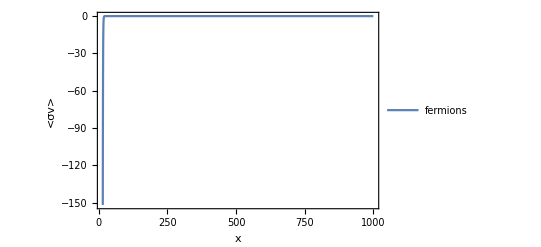

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},IntFermionsFunc[x]]} ,{x,15,1000},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

```mathematica
IntFermions
```

(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (-7 π^4 x^3 δ BesselK[3,x]-1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

```mathematica
(IntBosons-IntFermions)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (π^4 x^3 δ BesselK[3,x]+90 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

#### Putting together <σv>

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ]
```

```mathematica
nDM=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
σvAveragedFermions=(2 π^2)/(nDM nbFermions)IntFermions//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 δ BesselK[3,x]+1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermions/.δ->1//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedBosons=(2 π^2)/(nDM nbBosons)IntBosons//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+180 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(30 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
(σvAveragedFermions-σvAveragedBosons)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+270 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermionsFunc[y_]:=σvAveragedFermions/.x-> y;
σvAveragedBosonsFunc[y_]:=σvAveragedBosons/.x-> y;
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermionsFunc[30],10]]
```

-0.875739

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=0.1},N[σvAveragedFermions,10]]
```

-(0.919459518 (-1119.88 (6. x BesselK[1.,x]+(24.+x^2) BesselK[2.,x])+68.1864 x^3 BesselK[3.,x]))/(x^4 BesselK[2.,x])

#### Non-relativistic medium

From Gondolo & Gelmini

```mathematica
ClearAll[σvAveragedNR]
```

```mathematica
(σ0+σ1 s+σ2 s^2)/.σSeriesIns
```

(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π)

```mathematica
σvSeries
```

-(ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (-1+2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (1+δ)^2 (-1+2 δ))/(4 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+δ)^4 (-1+2 δ))/(8 MZp^4 π)

```mathematica
σvAveragedNR[x_]:=NIntegrate[(2 π^2 m/x σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1,{s,4 MD1^2,∞}]
σvAveragedNRAnalytical[x_]:=Integrate[(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m])/.σSeriesIns/.m-> MD1,{s,4 MD1^2,∞}]
```

```mathematica
Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNR[10]]
N[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNRAnalytical[10]] ,6]
```

4.41662×10^-6

ReplaceAll::reps: {σSeriesIns} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::inumr: The integrand 20 π^2 (-40000+s) √s (σ0+s σ1+s^2 σ2) BesselK[1,(√s)/10]/.σSeriesIns has evaluated to non-numerical values for all sampling points in the region with boundaries {{40001,41000}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate[20 π^2 (-40000+s) √s (σ0+s σ1+s^2 σ2) BesselK[1,(√s)/10]/.σSeriesIns,{s,40001,41000},WorkingPrecision→16.,AccuracyGoal→∞,PrecisionGoal→6.]

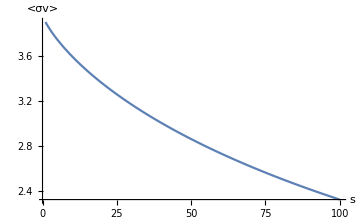

```mathematica
Plot[Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},(-2 π^2 m/x σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1/.x-> 10] ,{s,1,100},AxesLabel->{"s","<σv>"},ImageSize->Medium,PlotRange->All]
```

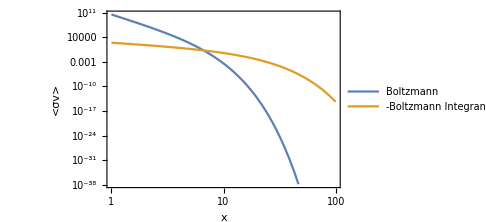

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[x]],Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},(-2 π^2 m/x σvSeries(s-4 m^2)√s BesselK[1,(√s x)/m])/.m-> MD1/.s-> 10^3]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"Boltzmann","-Boltzmann Integrand"},ImageSize->Medium]
```

```mathematica
σvAveragedNRAnalytical[1.5]
```

ConditionalExpression[259433.-1. (1.+4. MD1^2)^1.5 (-8.52541×10^13 HypergeometricPFQRegularized[{1.5},{2.,2.5},0.00005625+0.000225 MD1^2]+8.52541×10^13 HypergeometricPFQRegularized[{1.5},{2.5,2.},0.00005625+0.000225 MD1^2]), ]

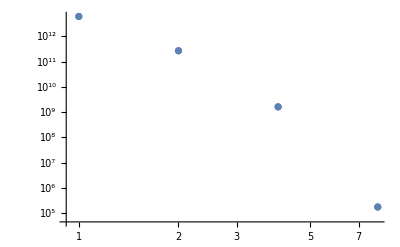

```mathematica
Show[ListLogLogPlot[Transpose[{PowerRange[1, 10,2],N[Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNRAnalytical[#]] ,6]&/@PowerRange[1, 10,2]}]],ListLogLogPlot[Transpose[{PowerRange[1, 10,2],N[Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNR[#]] ,6]&/@PowerRange[1, 10,2]}]]]
```

```mathematica
N[Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNRAnalytical[#]] ,6]/Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=1/2,stheta=1/2,MD1=100,δ=10^-2},σvAveragedNR[#]]&/@PowerRange[1, 10,2]
```

{1.,1.,1.,1.}

#### Plots

```mathematica
(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m])/.σSeriesIns/.m-> MD1
```

1/x 2 MD1 π^2 √s (-4 MD1^2+s) ((ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π)) BesselK[1,(√s x)/MD1]

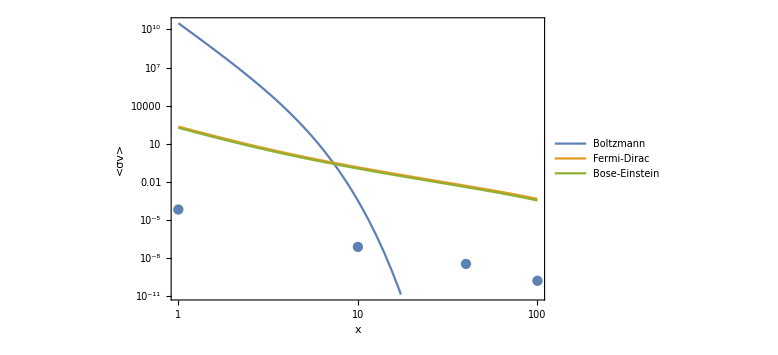

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=150,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=150,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=150,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedBosonsFunc[x]]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"Boltzmann","Fermi-Dirac","Bose-Einstein"},ImageSize->Large],ListLogLogPlot[listInt]]
```

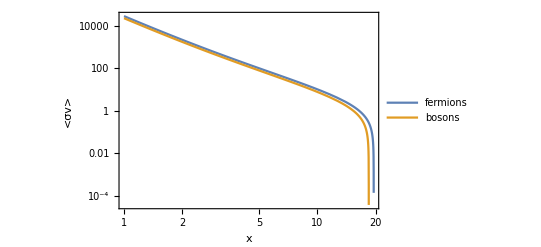

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

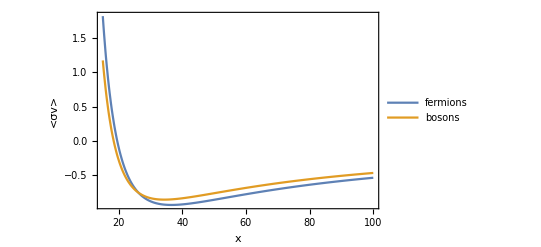

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,15,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

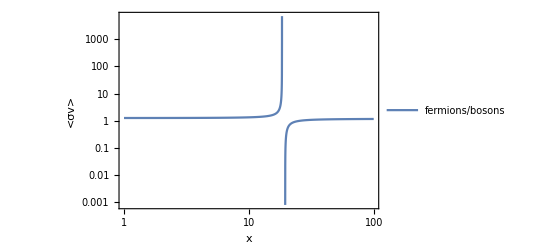

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]]/Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions/bosons"}]
```

```mathematica
Rasterize[LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.05},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.3},σvAveragedFermionsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"δ=0.05","δ=0.3"},ImageSize->Large]]
```

-Graphics-

```mathematica
ClearAll[plottingFunction]
```

```mathematica
δlist={0.01,0.5,1};
plottingFunction[x_]:=(Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5 ,MD1=100,δ=#},σvAveragedFermionsFunc[x]]&/@δlist);
Plot[plottingFunction[x],{x,0,1},PlotRange->All,PlotStyle->{"Red","Green","Blue"},PlotLegends->δlist,Frame->True,FrameLabel->{"x","<σv>"}]
```

-Graphics-

```mathematica
plottingFunction[x]
```

{-(0.91946 (-1119.88 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x])+68.1864 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (0.+340.932 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(x^4 BesselK[2,x])}

## Averaged cross section by integration over vrel, mx=MD1

```mathematica
σvSeriesvrel
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 vrel δ)/(4 MZp^4 π)+vrel^2 ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))

```mathematica
vrels=Solve[s==MD1^2(1+vrel/2),vrel][[1,1,2]]/.MD1-> mx
```

-(2 (mx^2-s))/mx^2

```mathematica
sfromθ=mx^2+2 Eb (Ex-√(Ex^2-mx^2)cosθ);
```

```mathematica
vrels/.s-> sfromθ/.cosθ-> 1
```

(4 Eb (Ex-√(Ex^2-mx^2)))/mx^2

```mathematica
vrels/.s-> sfromθ/.cosθ-> -1
```

(4 Eb (Ex+√(Ex^2-mx^2)))/mx^2

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},vrels/.s-> sfromθ/.cosθ-> -1]/.Ex-> 1000/.mx-> 100/.Eb-> 1000//N
```

797.995

Integration over s

```mathematica
vrelint=Collect[ Integrate[(σvrel1 vrel+σvrel2 vrel^2)(mx^2(1+vrel/2)-mx^2),{vrel,(vrels/.s-> sfromθ/.cosθ-> 1),(vrels/.s-> sfromθ/.cosθ->- 1)},Assumptions->assum],{σvrel1,σvrel2}]
```

((256 Eb^3 Ex^2 √(Ex^2-mx^2))/(3 mx^4)-(64 Eb^3 √(Ex^2-mx^2))/(3 mx^2)) σvrel1+((512 Eb^4 Ex^3 √((Ex-mx) (Ex+mx)))/mx^6-(256 Eb^4 Ex √((Ex-mx) (Ex+mx)))/mx^4) σvrel2

Integration over Eb - energy of a bath particle, separately for bosons and fermions (note that normalization number density is also different for these particles)

```mathematica
EbintFermions=Collect[Integrate[vrelint/(ⅇ^(Eb/T)+1),{Eb,0,∞},Assumptions->assum],{σvrel1,σvrel2}]
```

-(56 √(Ex^2-mx^2) (-4 Ex^2+mx^2) π^4 T^4 σvrel1)/(45 mx^4)-(5760 Ex √(Ex^2-mx^2) (-2 Ex^2+mx^2) T^5 σvrel2 Zeta[5])/mx^6

```mathematica
EbintBosons=Collect[Integrate[vrelint/(ⅇ^(Eb/T)-1),{Eb,0,∞},Assumptions->assum],{σvrel1,σvrel2}]
```

-(64 √(Ex^2-mx^2) (-4 Ex^2+mx^2) π^4 T^4 σvrel1)/(45 mx^4)-(6144 Ex √(Ex^2-mx^2) (-2 Ex^2+mx^2) T^5 σvrel2 Zeta[5])/mx^6

Integration over Ex - energy of the DM particle (takes forever to calculate)

```mathematica
Join[assum,Element[{σvrel1,σvrel2}, Reals]]
```

Join[{ME>0&&MD1>0&&MD2>0&&MZ>0&&MZp>0&&vrel>0&&del>0&&T>0&&(MD1|MD2|MZ|MZp|sa|sw|ca|eta|chi|vrel|del|ME|T)∈ℝ},(σvrel1|σvrel2)∈ℝ]

```mathematica
(*ExintFermions=Collect[Integrate[EbintFermions ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->Join[assum,Element[{σvrel1,σvrel2}, Reals]]],{σvrel1,σvrel2}]*)
```

$Aborted

```mathematica
ExintFermions=(56 π^4 T^5 BesselK[3,mx/T])/(15 mx)σvrel1+(5760 T^6 σvrel2 BesselK[4,mx/T] Zeta[5])/mx^2;
```

```mathematica
(*ExintBosons=Collect[Integrate[EbintBosons ⅇ^(-Ex/T),{Ex,mx,∞},Assumptions->assum],{σvrel1,σvrel2}]*)
```

#### Plugging in the cross section expansion coefficients

```mathematica
coef={σvrel1-> -(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(4 MZp^4 π),σvrel2-> ((ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2)/(32 MZp^4 π)-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 δ)/(16 MZp^4 π))//FullSimplify};
```

```mathematica
IntBosons=ExintBosons/.mx-> MD1/.coef/.T-> MD1/x//FullSimplify;
```

```mathematica
IntFermions=ExintFermions/.mx-> MD1/.coef/.T-> MD1/x//FullSimplify
```

-(2 ctheta^2 EE^2 eps^2 gX^2 MD1^6 stheta^2 (7 π^4 x δ BesselK[3,x]+1350 (-1+2 δ) BesselK[4,x] Zeta[5]))/(15 MZp^4 π x^6)

```mathematica
IntFermionsFunc[y_]:=IntFermions/.x-> y;
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},IntFermionsFunc[10]]
```

-14.2311

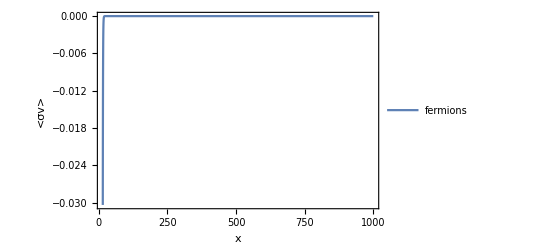

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.2},IntFermionsFunc[x]]} ,{x,15,1000},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

```mathematica
IntFermions
```

```mathematica
(IntBosons-IntFermions)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^8 stheta^2 (π^4 x^3 δ BesselK[3,x]+90 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(15 MZp^4 π x^8)

#### Putting together <σv>

```mathematica
ClearAll[EE,eps,MZp,gX,ctheta,stheta,MD1,δ]
```

```mathematica
nDM=4 π gDM MD1^2 T BesselK[2,MD1/T]/.T-> MD1/x;
nbFermions=6 π gb Zeta[3] T^3/.T-> MD1/x;
nbBosons=8 π gb Zeta[3] T^3/.T-> MD1/x;
```

```mathematica
σvAveragedFermions=(2 π^2)/(nDM nbFermions)IntFermions//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 δ BesselK[3,x]+1350 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermions/.δ->1//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedBosons=(2 π^2)/(nDM nbBosons)IntBosons//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+180 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(30 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
(σvAveragedFermions-σvAveragedBosons)//FullSimplify
```

-(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (π^4 x^3 δ BesselK[3,x]+270 (-1+2 δ) (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(180 gb gDM MZp^4 π x^4 BesselK[2,x] Zeta[3])

```mathematica
σvAveragedFermionsFunc[y_]:=σvAveragedFermions/.x-> y;
σvAveragedBosonsFunc[y_]:=σvAveragedBosons/.x-> y;
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=1},σvAveragedFermionsFunc[30]]
```

-24.4224

#### Non-relativistic medium

From Gondolo & Gelmini

```mathematica
ClearAll[σvAveragedNR]
```

```mathematica
σvAveragedNR[x_]:=NIntegrate[(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m]/.σSeriesIns/.m-> MD1),{s,4 MD1^2,∞}]
```

```mathematica
Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedNR[100]]
```

1.2535×10^-77

#### Plots

```mathematica
(2 π^2 m/x(σ0+σ1 s+σ2 s^2)(s-4 m^2)√s BesselK[1,(√s x)/m])/.σSeriesIns/.m-> MD1
```

1/x 2 MD1 π^2 √s (-4 MD1^2+s) ((ctheta^2 EE^2 eps^2 gX^2 s^2 stheta^2 (1-2 δ))/(8 MD1^2 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 MD1^2 stheta^2 (1+2 δ))/(8 MZp^4 π)+(ctheta^2 EE^2 eps^2 gX^2 s stheta^2 (MD1^2 (-1+2 δ)-MD1^2 (1+2 δ)))/(8 MD1^2 MZp^4 π)) BesselK[1,(√s x)/MD1]

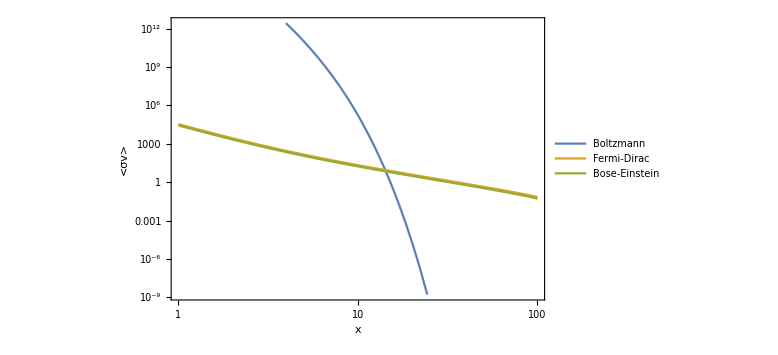

```mathematica
Show[LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedNR[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.01},σvAveragedBosonsFunc[x]]} ,{x,1,100},Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"Boltzmann","Fermi-Dirac","Bose-Einstein"},ImageSize->Large]]
```

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

-Graphics-

```mathematica
Plot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,15,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions","bosons"}]
```

-Graphics-

```mathematica
LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedFermionsFunc[x]]/Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.1},σvAveragedBosonsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"fermions/bosons"}]
```

-Graphics-

```mathematica
Rasterize[LogLogPlot[{Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.05},σvAveragedFermionsFunc[x]],Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5,MD1=100,δ=0.3},σvAveragedFermionsFunc[x]]} ,{x,1,100},PlotRange->All,Frame->True,FrameLabel->{"x","<σv>"},PlotLegends->{"δ=0.05","δ=0.3"},ImageSize->Large]]
```

-Graphics-

```mathematica
ClearAll[plottingFunction]
```

```mathematica
δlist={0.01,0.5,1};
plottingFunction[x_]:=(Block[{EE=1,eps=1,MZp=1,gX=1,gb=1,gDM=1,ctheta=0.5,stheta=0.5 ,MD1=100,δ=#},σvAveragedFermionsFunc[x]]&/@δlist);
Plot[plottingFunction[x],{x,0,1},PlotRange->All,PlotStyle->{"Red","Green","Blue"},PlotLegends->δlist,Frame->True,FrameLabel->{"x","<σv>"}]
```

-Graphics-

```mathematica
plottingFunction[x]
```

{-(0.91946 (-1119.88 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x])+68.1864 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (0.+340.932 x^3 BesselK[3,x]))/(x^4 BesselK[2,x]),-(0.91946 (7 π^4 x^3 BesselK[3,x]+1350 (6 x BesselK[1,x]+(24+x^2) BesselK[2,x]) Zeta[5]))/(x^4 BesselK[2,x])}